-Graphics-

```mathematica
col={Hue[0,.3],Hue[.17,.3],Hue[.6,.3]};
```

```mathematica
pic[L_]:=Style[Graphics[{
MapIndexed[{col[[#1]],Rectangle[#2-1,#2]}&,L,{2}],
Table[Line[{{0,i},{Length[L],i}}],{i,0,Length[L[[1]]]}],
Table[Line[{{i,0},{i,Length[L[[1]]]}}],{i,0,Length[L]}]},ImageSize->15Length[L]],Antialiasing->False]
```

```mathematica
randomperm[L_]:=Transpose[Sort[Transpose[{Table[Random[],{Length[L]}],L}]]][[2]]
```

```mathematica
dokay[L_,t_]:=Complement[t,Accumulate[Map[Length,L]]]=={}
```

```mathematica
chop[L_]:=Module[{stac},
stac={{L,{}}};
solns={};
While[Length[stac]>0,
cur=First[stac];
stac=Rest[stac];
pos=First[cur];
If[pos=={},AppendTo[solns,Last[cur]]];
If[Length[pos]≥width,PrependTo[stac,{Drop[pos,width],Append[Last[cur],Take[pos,width]]}]];
If[Length[pos]≥height,PrependTo[stac,{Drop[pos,height],Append[Last[cur],Take[pos,height]]}]]];solns]
```

```mathematica
jive[L_]:=Module[{},
long=Permutations[Select[L,Length[#]==width&]];
short=Sort[Select[L,Length[#]==height&]];
Select[long,Sort[Transpose[#]]==short&]]
```

```mathematica
parti[L_]:=Module[{LL,lens,places,i},
LL={L};
lens=Accumulate[Map[Length,L]];
places=Map[{#[[1]]+1,#[[2]]}&,Partition[Flatten[Join[{0},Position[Map[Mod[#,n]&,lens],0]]],2,1]];
Map[Take[L,#]&,places]]
```

```mathematica
boldpic[L_,d_]:=Style[Graphics[{
MapIndexed[{col[[#1]],Rectangle[#2-1,#2]}&,L,{2}],
Table[Line[{{0,i},{Length[L],i}}],{i,0,Length[L[[1]]]}],
Table[Line[{{i,0},{i,Length[L[[1]]]}}],{i,0,Length[L]}],
AbsoluteThickness[3],Table[Line[{{0,i},{Length[L],i}}],{i,0,Length[L[[1]]]}],MapIndexed[Line[{{#1,#2[[1]]-1},{#1,#2[[1]]}}]&,Map[Prepend[Accumulate[#],0]&,Map[Length,parti[Select[CH,jive[#]=!={}&][[1]]],{2}]],{2}]
},ImageSize->15Length[L]],Antialiasing->False]
```

```mathematica
For[k=1,k≤100,k++,
width=10;
height=5;
n=20;
L=Table[RandomInteger[{1,3}],{width},{height}];
If[Min[Table[Count[Flatten[L],i],{i,1,3}]]≥height width/4,
R=randomperm[Sort[Transpose[L]~Join~L]];
While[Not[dokay[R,Table[i,{i,n,2width height,n}]]],R=randomperm[Sort[Transpose[L]~Join~L]]];P=Partition[Flatten[R],n,n];
CH=Select[Flatten[Outer[Join,Apply[Sequence,Map[chop,P]],1],2width height/n -1],Sort[Map[Length,#]]==Table[height,{width}]~Join~Table[width,{height}]&];
If[Length[Flatten[Map[jive,CH],1]]==1,Print[];Print[pic[Transpose[P]]];Print[boldpic[Transpose[P],CH]];Print[pic[Map[Reverse,L]]]];]]
```

## 8 = 4x2 (8x2)

-Graphics-

-Graphics-

-Graphics-

## 18 = 6x3 (9x4)

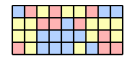

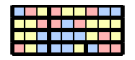

-Graphics-

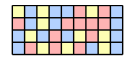

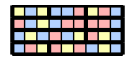

-Graphics-

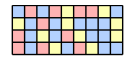

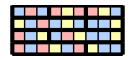

-Graphics-

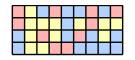

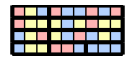

-Graphics-

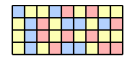

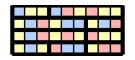

-Graphics-

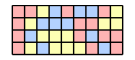

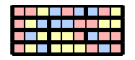

-Graphics-

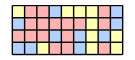

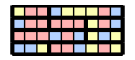

-Graphics-

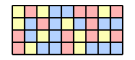

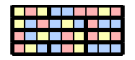

-Graphics-

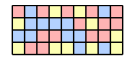

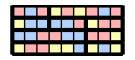

-Graphics-

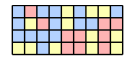

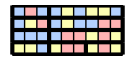

-Graphics-

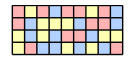

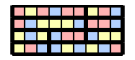

-Graphics-

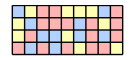

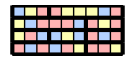

-Graphics-

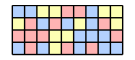

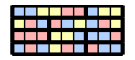

-Graphics-

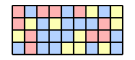

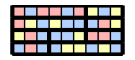

-Graphics-

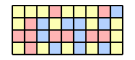

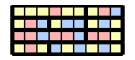

-Graphics-

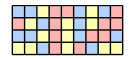

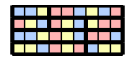

-Graphics-

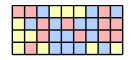

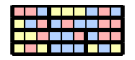

-Graphics-

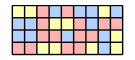

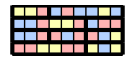

-Graphics-

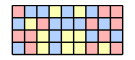

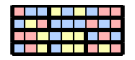

-Graphics-

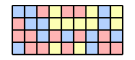

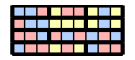

-Graphics-

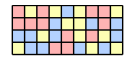

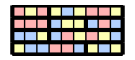

-Graphics-

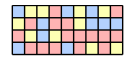

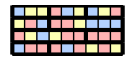

-Graphics-

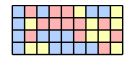

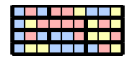

-Graphics-

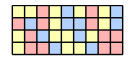

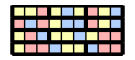

-Graphics-

## 24 = 6x4 (16x3)

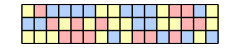

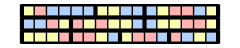

-Graphics-

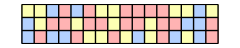

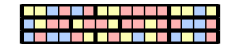

-Graphics-

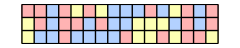

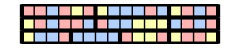

-Graphics-

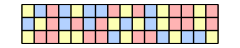

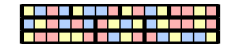

-Graphics-

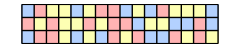

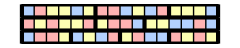

-Graphics-

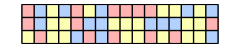

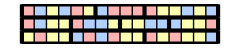

-Graphics-

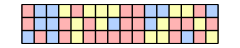

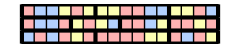

-Graphics-

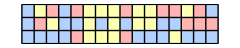

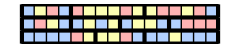

-Graphics-

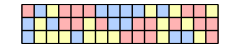

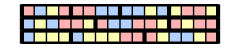

-Graphics-

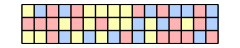

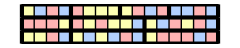

-Graphics-

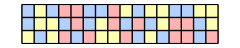

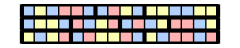

-Graphics-

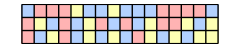

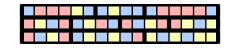

-Graphics-

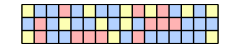

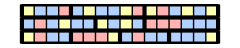

-Graphics-

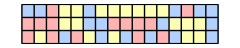

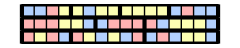

-Graphics-

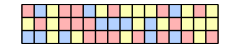

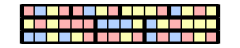

-Graphics-

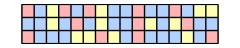

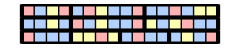

-Graphics-

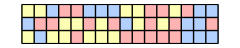

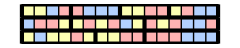

-Graphics-

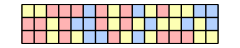

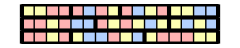

-Graphics-

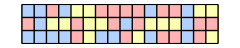

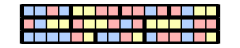

-Graphics-

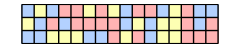

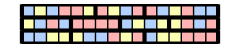

-Graphics-

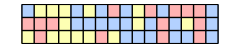

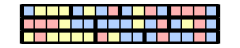

-Graphics-

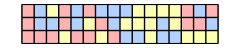

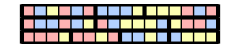

-Graphics-

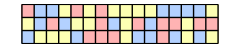

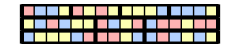

-Graphics-

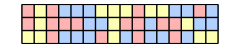

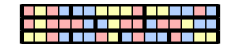

-Graphics-

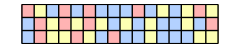

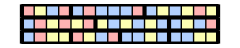

-Graphics-

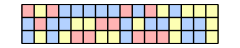

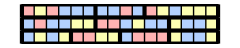

-Graphics-

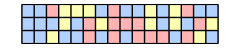

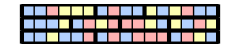

-Graphics-

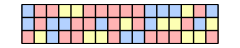

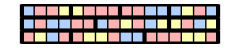

-Graphics-

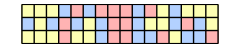

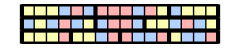

-Graphics-

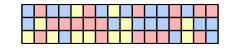

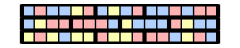

-Graphics-

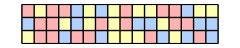

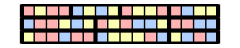

-Graphics-

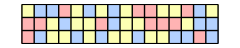

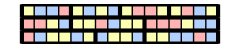

-Graphics-

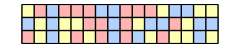

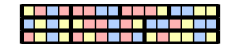

-Graphics-

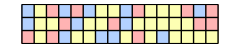

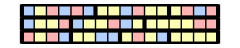

-Graphics-

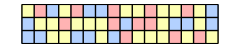

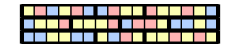

-Graphics-

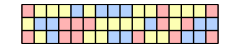

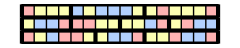

-Graphics-

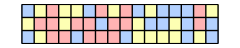

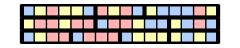

-Graphics-

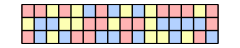

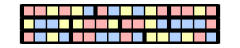

-Graphics-

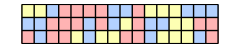

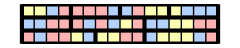

-Graphics-

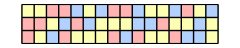

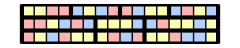

-Graphics-

-Graphics-

-Graphics-

«34 more identical outputs»

## 27 = 9x3 (18x3)

-Graphics-

-Graphics-

-Graphics-

«135 more identical outputs»

## 32 = 8x4 (16x4)

-Graphics-

-Graphics-

-Graphics-

«168 more identical outputs»

## 48 = 8x6 (24x4)

-Graphics-

-Graphics-

-Graphics-

«222 more identical outputs»

## 50 = 10x5 (20x5)

-Graphics-

-Graphics-

-Graphics-

«234 more identical outputs»